```mathematica
x={0.8768,0.8750,0.883,0.890,0.897,0.895,0.880,0.847,0.877,0.830,0.865,0.862,0.880,0.810,0.800,0.805}
```

{0.8768,0.875,0.883,0.89,0.897,0.895,0.88,0.847,0.877,0.83,0.865,0.862,0.88,0.81,0.8,0.805}

```mathematica
xerror={0.0069,0.0068,0.014,0.014,0.018,0.010,0.015,0.008,0.024,0.040,0.020,0.012,0.030,0.020,0.025,0.011}
```

{0.0069,0.0068,0.014,0.014,0.018,0.01,0.015,0.008,0.024,0.04,0.02,0.012,0.03,0.02,0.025,0.011}

```mathematica
plotxvalues=Table[Around[x[[i]],xerror[[i]]],{i,1,Length[x]}]
```

{0.8770.007,0.8750.007,0.8830.014,0.8900.014,0.8970.018,0.8950.010,0.8800.015,0.8470.008,0.8770.024,0.830.04,0.8650.020,0.8620.012,0.8800.030,0.8100.020,0.8000.025,0.8050.011}

```mathematica
y={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

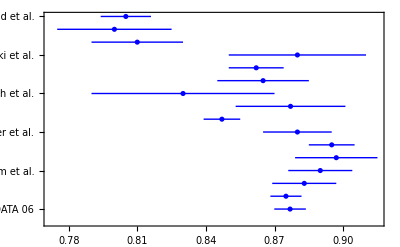

```mathematica
b=ListPlot[Transpose[{plotxvalues,y}],PlotStyle->Blue, Frame->True, Joined->{False, True},FrameTicks->{Automatic,{{1,"CODATA 06"},{2,"CODATA 02"},{3,"Melnikov et al."},{4,"Udem et al."},{5,"Blunden et al."},{6,"Sick et al."},{7,"Rosenfelder et al."},{8,"Mergell et al."},{9,"Wong et al."},{10,"Eschrich et al."},{11,"McCord et al."},{12,"Simon et al."},{13,"Borkowski et al."},{14,"Akimov et al."},{15,"Frerejacque et al."},{16,"Hand et al."}}}]
```

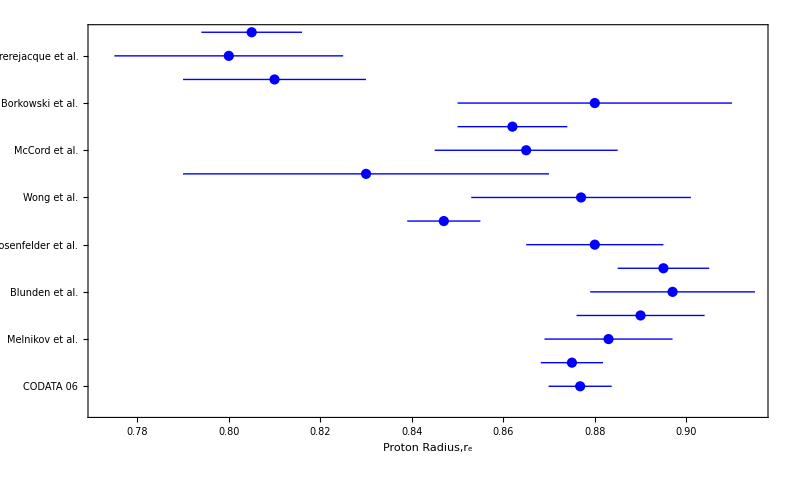

```mathematica
Show[b,FrameLabel->{"Proton Radius,r_e",""},LabelStyle->{FontFamily->"Arial",14,GrayLevel[0]},AxesStyle->Black,ImageSize->800]
```